If[x≥0,x,0]

0

0

0.117674+1.38032 If[0.521418+0.777443 x-0.891345 y≥0,0.521418+0.777443 x-0.891345 y,0]-0.365027 If[0.539162+0.957569 x-0.817436 y≥0,0.539162+0.957569 x-0.817436 y,0]+0.00707785 If[-0.62264+0.00891098 x-0.525165 y≥0,-0.62264+0.00891098 x-0.525165 y,0]+0.462966 If[-0.416591+0.564574 x-0.436715 y≥0,-0.416591+0.564574 x-0.436715 y,0]+0.285403 If[0.573253-0.460578 x-0.252597 y≥0,0.573253-0.460578 x-0.252597 y,0]-0.391557 If[-0.0925501+0.01282 x-0.154967 y≥0,-0.0925501+0.01282 x-0.154967 y,0]-0.639519 If[0.232912-0.181639 x-0.150228 y≥0,0.232912-0.181639 x-0.150228 y,0]-0.445129 If[-0.251981-0.487997 x-0.148412 y≥0,-0.251981-0.487997 x-0.148412 y,0]-0.58112 If[0.214579-0.403112 x-0.14715 y≥0,0.214579-0.403112 x-0.14715 y,0]+0.0943596 If[0.870624-0.543243 x-0.0789416 y≥0,0.870624-0.543243 x-0.0789416 y,0]+0.149593 If[-0.861317+0.175052 x+0.0198112 y≥0,-0.861317+0.175052 x+0.0198112 y,0]-0.779756 If[-0.362411-0.526657 x+0.0210741 y≥0,-0.362411-0.526657 x+0.0210741 y,0]+0.666438 If[0.502587-0.0220142 x+0.188837 y≥0,0.502587-0.0220142 x+0.188837 y,0]+0.203813 If[0.0193255-0.410675 x+0.345788 y≥0,0.0193255-0.410675 x+0.345788 y,0]-0.961649 If[-0.563611-0.615741 x+0.551123 y≥0,-0.563611-0.615741 x+0.551123 y,0]+0.524351 If[-0.201218-1.44218 x+1.25433 y≥0,-0.201218-1.44218 x+1.25433 y,0]

-0.0191425

-0.0191425

-0.0199309+0.397084 If[-0.0655698-0.0733115 x-1.42518 y≥0,-0.0655698-0.0733115 x-1.42518 y,0]-0.650916 If[-1.26024-0.175484 x-1.38973 y≥0,-1.26024-0.175484 x-1.38973 y,0]+0.00335256 If[0.0185853+0.0441549 x-0.958007 y≥0,0.0185853+0.0441549 x-0.958007 y,0]+1.66073 If[0.00892467-0.737115 x-0.283334 y≥0,0.00892467-0.737115 x-0.283334 y,0]-1.61726 If[-1.40353+0.0687461 x-0.225587 y≥0,-1.40353+0.0687461 x-0.225587 y,0]+1.44156 If[-1.51056+0.107538 x-0.21891 y≥0,-1.51056+0.107538 x-0.21891 y,0]+0.00345545 If[-1.48922-0.306356 x+0.224401 y≥0,-1.48922-0.306356 x+0.224401 y,0]+0.00241235 If[-2.22757-0.120315 x+0.339618 y≥0,-2.22757-0.120315 x+0.339618 y,0]

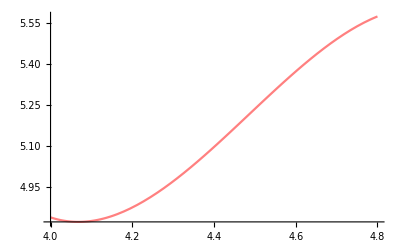

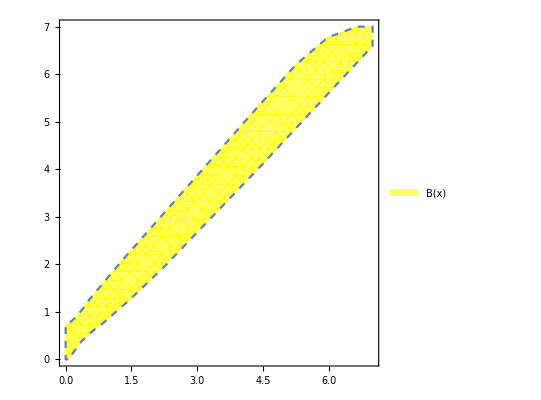

print[g_b]

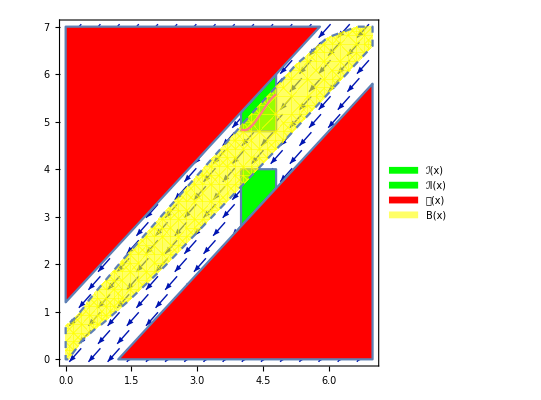

-Graphics-

```mathematica
(*phi=RegionPlot[(x≥0&&x≤0.7&&y≥0.7&&y≤1.5&&y-x<=0.8),{x,0,0.7},{y,0.7,1.5},PlotPoints->50,BoundaryStyle->Directive[RGBColor[0,0.5,0], Thin],PlotStyle->Directive[Blue]]
(*phi ->initial region *)
psi1=RegionPlot[(x≥0&&x≤8&&y≥0&&y≤8&&(y-x)*(y-x)>=1),{x,0,8},{y,0,8},PlotPoints->70,PlotStyle->Directive[Red],BoundaryStyle->Directive[RGBColor[0.5,0,0], Opacity[0.05],Thin]]*)
(* we first give ReLU fuction*)
clc;
relu[x_] =If[x>=0,x,0]
(*psi -> unsafe region*)

(*B(x,xˆ)=0.9227x1*x1+0.2348v1*v1+0.9227x2*x2+0.2348v2*v2+0.006x1*v1−0.006x2*v1−0.006x1*v2−0.006x2*v2−0.4696v1*v2−1.845x1x2−0.0002*x2+0.0728,*)
(* this B is only for test*)
(*bc=0.9227*x*x + 0.9227*y*y -1.845*x*y  - 0.0002*y + 0.0728*)
x3 =0
x4 =0
(*bc = 0.20961230198452*relu[-0.977049978594831*x+0.838193844644194*y+0.673876516960258*x3+0.109865833801004*x4-0.114489667236974]+0.808674414424979*relu[-0.920933153368576*x+1.0062890970721*y-0.176760617228555*x3-0.791901874763677*x4-0.80873469159142]+0.162688373479436*relu[-0.646939421973636*x-0.760381318212942*y-0.666733754645751*x3+1.10370677691161*x4-0.358373162848607]-0.214726527857423*relu[-0.631802584773815*x-1.25178201852823*y-0.428297763637914*x3-0.114215633343116*x4+0.0372529696741055]-0.588395098985064*relu[-0.438681329735811*x-0.297975477898638*y+0.819519236154835*x3+1.53348787259804*x4-0.80622951192207]-0.139058288108177*relu[-0.434578340477944*x-0.475074447140696*y+1.2421679896633*x3+0.0333438417047977*x4-0.231353974340392]-0.183939396623495*relu[-0.424401945870926*x-1.66951018848325*y-0.442102734664958*x3+1.15142783054075*x4-0.0856033743036387]+0.515810270350256*relu[-0.0759138015466691*x+0.0471124902336029*y+0.622074417936798*x3-1.39449843558552*x4+0.651846180792139]+0.210595044988341*relu[-0.0694247105713332*x+0.731764561611308*y-0.503922656752624*x3+0.220967691080613*x4-0.594955377646663]+0.662138647080873*relu[0.0041198681508566*x+0.00135418297968122*y-0.629424928923776*x3-2.18001913904973*x4+0.403642994711347]-0.470780188729511*relu[0.206887832104576*x+0.0570308966072177*y-0.676184169437032*x3+1.50096662080654*x4+0.0362796343748758]-0.838503405113198*relu[0.533126650747215*x-0.54246887065665*y+0.137735538072937*x3-0.976123412853063*x4+0.576685939853719]+0.859452298831454*relu[0.656812512439823*x+0.166080901133304*y-0.254409504485466*x3-1.27516494453622*x4-0.713010049749584]+0.948981746083281*relu[1.00455001805316*x-0.797702269559013*y-0.726660024423718*x3+0.133951257645475*x4+0.479134377762676]-0.0506009606268825*relu[1.04877726296366*x-0.109361246682383*y+0.502806354258896*x3-0.236434097910047*x4+0.091177127429201]-0.51739630585403*relu[1.11125252441803*x-0.650703734377074*y+0.233534388896706*x3-0.528959456589365*x4-1.28212192477566]+0.414080290559346*)
bc = 0.524351078903926*relu[-1.44217705195367*x+1.25432616785563*y-0.407778024200744*x3+0.228657041948259*x4-0.201218088789752]-0.96164946093654*relu[-0.615740525370689*x+0.551123248696316*y-0.416778824564777*x3-0.69706511899961*x4-0.563610614014081]+0.0943595700677426*relu[-0.543242808808419*x-0.0789416184146183*y+0.476800035454634*x3-0.142763675399842*x4+0.870624341589244]-0.779756350789702*relu[-0.52665669274311*x+0.021074130077308*y-0.0378118498599886*x3+0.159204988801668*x4-0.362411383165029]-0.445128509070559*relu[-0.487996888726357*x-0.148411526046678*y+0.167589192311535*x3-0.354147385445193*x4-0.251981478319987]+0.285402578323149*relu[-0.460578022748923*x-0.252596925469704*y+0.270688873452909*x3-0.00694242889178447*x4+0.573252604019007]+0.203812677169878*relu[-0.410674850941398*x+0.345788137440833*y+0.298720413607938*x3-0.0464265113360287*x4+0.0193255402231361]-0.581119927417328*relu[-0.403112483099412*x-0.14715002335707*y+0.501324562022139*x3+0.392359170708008*x4+0.214579030323118]-0.639518832581957*relu[-0.181638838384871*x-0.150228273764364*y-0.0754602780633407*x3-0.70552619537272*x4+0.232911765447852]+0.666438387627093*relu[-0.0220142177822758*x+0.188837135674323*y+1.39965331267552*x3+1.87417801962028*x4+0.502586737853142]+0.00707785337945945*relu[0.00891097658428686*x-0.525165317310096*y+0.294314903869784*x3-0.160655147270086*x4-0.622640221673208]-0.391556897624477*relu[0.0128199504038893*x-0.154966850387391*y+0.189035789785861*x3+0.322312908481576*x4-0.0925500626104045]+0.149593398911215*relu[0.175052195913414*x+0.0198112214410646*y-0.25229960332363*x3+0.243238954454477*x4-0.861316692314903]+0.462966365545755*relu[0.564573814032393*x-0.436714625174316*y+1.10785907906393*x3+0.250698166346699*x4-0.41659066929971]+1.38031653216889*relu[0.777442658682152*x-0.891345374083048*y-0.00950443028666293*x3+1.8729970125365*x4+0.521418172107499]-0.365027137472273*relu[0.95756948983834*x-0.817435867044873*y-0.657152497717248*x3-0.0203806773300951*x4+0.539161860712748]+0.117674128415388
(*uˆ(x,ˆx,u)=0.8x1−0.8x2+1.5ˆx1−1.5ˆx2+u.*)
(*this is controller*)

(* xuebai *)
initialPlot=RegionPlot[(x≥4&&x≤4.8&&y≥4.8&&y≤6&&y-x<=1.2),{x,4,4.8},{y,4.8,6},PlotStyle->Directive[Green],PlotLegends->SwatchLegend[{"ℐ(x)"}]];
initialPlott=RegionPlot[(x≥4&&x≤4.8&&y≥2.8&&y≤4&&x-y<=1.2),{x,4,4.8},{y,2.8,4},PlotStyle->Directive[Green],PlotLegends->SwatchLegend[{"ℐI(x)"}]];
unsafePlot=RegionPlot[(x≥0&&x≤7&&y≥0&&y≤7&&(y-x)*(y-x)>=1.2*1.2),{x,0,7},{y,0,7},PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x)"}]];
bcPlot=RegionPlot[(x≥0&&x≤7&&y≥0&&y≤7&&bc<=1),{x,0,7},{y,0,7},BoundaryStyle->{Dashed},PlotStyle->Directive[Opacity[.6],Yellow],PlotLegends->SwatchLegend[{"B(x)"}]];
u = Random[Real,{-0.02,-0.018}]
x5 = u
(*uhat = 0.8*x+1.5*y+u*)
(*uhat  = -0.820000366275061*relu[-1.25655286488722*x-1.03813921537532*y+0.380053990335269*x3-0.552455077103081*x4+1.25493600710337*x5-0.112660563425455]-0.716081036328255*relu[-0.543847433985733*x+0.0561651546787756*y-0.2360780966606*x3-0.223898859850695*x4-0.468709844889*x5-0.449735858963336]+0.00879223688096601*relu[-0.523680074455316*x-0.512522647724036*y+0.844342222380732*x3+1.69978278136429*x4+1.36122800893796*x5+0.680799322745128]-0.0108096921452454*relu[-0.467729970730655*x-1.02691968899126*y-0.447488377323604*x3-1.6782702951372*x4-0.0804528021813899*x5+1.18773411395372]-0.00134205109973808*relu[-0.244371174775303*x+0.0312013790843017*y+0.533838850801307*x3+0.677562559847851*x4-0.847794538318824*x5-0.203919719944836]+0.0330705499764603*relu[0.0223543167842997*x-0.255475240540571*y+0.487890723272797*x3-1.09005781756055*x4+1.56616126778349*x5-0.278803403305047]-0.0190013133836391*relu[0.112848302303559*x-1.65411303909963*y-1.98594511828365*x3+1.27084697562287*x4-0.351370538474346*x5+0.173958195637829]+0.0230556355800742*relu[0.153174502593987*x-0.848573693930795*y+1.16246306785423*x3+0.548994077012214*x4+1.17476049203854*x5-0.961747901244111]+0.0455006565279379*)
uhat = 1.66072622866388*relu[-0.737115056618919*x-0.283333836479221*y+1.61814426461345*x3+0.439541151487422*x4-0.604675159420894*x5-0.00265034358721605]+0.00345544987880607*relu[-0.306355932960885*x+0.224400512116449*y+0.0550078152232705*x3-1.24275692504471*x4+0.587432183800198*x5-1.47797759459252]-0.650916369967446*relu[-0.175483749337114*x-1.38973272189551*y+0.547630318624378*x3+1.38077303619873*x4+1.16468923779223*x5-1.23794118287108]+0.00241234733524615*relu[-0.120314857611376*x+0.339617784612894*y+0.590641681021882*x3+0.29788976898321*x4+0.415729400691342*x5-2.21961686192657]+0.397083986912669*relu[-0.0733115458373732*x-1.42518210278342*y-1.01073992744236*x3+0.234379949775006*x4-0.475416248291621*x5-0.0746705033806877]+0.00335256135900997*relu[0.0441549240388186*x-0.958006727893888*y-0.134795208063172*x3-0.410284740466141*x4+0.247673609818938*x5+0.0233264192903776]-1.61726058804782*relu[0.0687460506360292*x-0.225587413588054*y+0.00872053679112974*x3+1.09781178033686*x4-0.414152126213077*x5-1.41146179853834]+1.4415566144234*relu[0.107538461815471*x-0.21891011980685*y-0.196482189316215*x3+0.665313056579903*x4+2.55781143858709*x5-1.46160129961965]-0.0199308739479114
flowPlot=VectorPlot[{x3*x3+u,x4*x4+uhat},{x,0,7},{y,0,7},VectorStyle->{Arrowheads[0.02],Blue}];
(*Vector=StreamPlot[{0.1+0.5*u, 0.1+0.5*uhat},{x,0,8},{y,0,8},StreamScale->0.16,StreamStyle->Gray]*)

(*domain1 = ContourPlot[V==0.048,{x,0,0.7},{y,0.7,1.5},ContourStyle->Directive[Black]]
domain3= ContourPlot[V==0.048,{x,0,8},{y,0,8},ContourStyle->Directive[blue]]*)
inpolt = Plot[{-2.7083*x*x*x +36.4375*x*x -162 * x + 243.17},{x,4,4.8},PlotStyle->Directive[Pink]]
g_b = Show[bcPlot]
print[g_b]

graphics=Show[flowPlot,initialPlot,initialPlott,unsafePlot,bcPlot,inpolt]
Print[graphics];
```

```mathematica
|
```